(0. | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.5 | 0. | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.5 | 0. | 0.5 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.5 | 0. | 0.5 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.5 | 0. | 0.5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.5 | 0. | 0.5 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.5 | 0. | 0.5 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0. | 0.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0. | 0.5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0.)

{{8.,17.,14.,12.,10.,8.,6.,4.,2.,1.},{8.5,11.,14.5,12.,10.,8.,6.,4.,2.5,1.},{5.5,11.5,11.5,12.25,10.,8.,6.,4.25,2.5,1.25},{5.75,8.5,11.875,10.75,10.125,8.,6.125,4.25,2.75,1.25},{4.25,8.8125,9.625,11.,9.375,8.125,6.125,4.4375,2.75,1.375},{4.40625,6.9375,9.90625,9.5,9.5625,7.75,6.28125,4.4375,2.90625,1.375},{3.46875,7.15625,8.21875,9.73438,8.625,7.92188,6.09375,4.59375,2.90625,1.45313},{3.57813,5.84375,8.44531,8.42188,8.82813,7.35938,6.25781,4.5,3.02344,1.45313},{2.92188,6.01172,7.13281,8.63672,7.89063,7.54297,5.92969,4.64063,2.97656,1.51172},{3.00586,5.02734,7.32422,7.51172,8.08984,6.91016,6.0918,4.45313,3.07617,1.48828}}

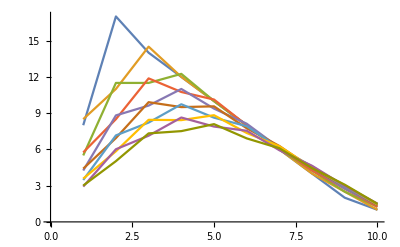

```mathematica
(*William Rodrigues*)

(*1. Execute the example from the text using forward Euler method. Take ↵=1/2,the spatial interval as[5,5],x=0 .1,t=0 .01.For the initial state take u(xi,0)=0 for every i and for the boundary values take each u(5,tn)=20 and u(5,tn)=0. Plot the temperatures at t=0*)

a=.5;
delx=.1;
delt=.01;
l=.5;
u={20,16,14,12,10,8,6,4,2,0};
Matt={};
For[i=0,i<10,i++,
row={};
For[j=0,j<10,j++,
If[i==j,
AppendTo[row,1-2l],
If[i==j-1||j==i-1,
AppendTo[row,l],
AppendTo[row,0]
];
];
];
AppendTo[Matt,row]
];
Print[MatrixForm[Matt]]

un={};
n=10;
For[i=1,i≤n,i++,
var=Matt.u;
u=var;
AppendTo[un,u];
];

Print[un]
ListLinePlot[un]
```

(-3 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -3 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | -3 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | -3 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | -3 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | -3 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | -3 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | -3 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -3 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -3)

{{-28,20,14,12,10,8,6,4,2,4},{124,-88,22,12,10,8,6,4,10,-8},{-548,556,-218,28,10,8,6,20,-38,44},{2756,-3200,1822,-500,42,8,38,-124,242,-208},{-14668,18756,-12866,5228,-1110,136,-346,932,-1390,1108},{81516,-111336,86566,-43636,14058,-3320,3174,-6268,8250,-6104},{-467220,670172,-569642,332156,-136086,44424,-28698,41652,-49494,34812},{2742004,-4084240,3713582,-2407924,1161418,-462840,258246,-281340,301410,-203424},{-16394492,25163892,-24125074,16973772,-9225782,4227848,-2263098,1963332,-1873758,1213092},{99511260,-156530808,156650550,-117623028,70080586,-35661304,19171654,-14163708,11974122,-7386792}}

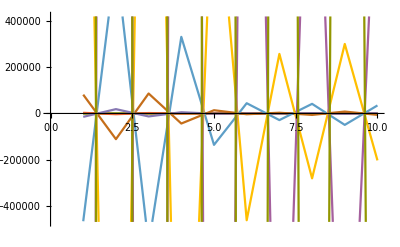

```mathematica
(*2. Redo Problem 1 with ↵=2. Notice that the results are not well behaved.The problem here is that the forward Euler method is not stable then>0.5.Stability of transient or time dependent processes is covered in following section.*)
a=2;
delx=.1;
delt=.01;
l=2;
u={20,16,14,12,10,8,6,4,2,0};
Matt={};
For[i=0,i<10,i++,
row={};
For[j=0,j<10,j++,
If[i==j,
AppendTo[row,1-2l],
If[i==j-1||j==i-1,
AppendTo[row,l],
AppendTo[row,0]
];
];
];
AppendTo[Matt,row]
];
Print[MatrixForm[Matt]]

un={};
n=10;
For[i=1,i≤n,i++,
var=Matt.u;
u=var;
AppendTo[un,u];
];

Print[un]
ListLinePlot[un]
```

(0.6 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.2 | 0.6 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2 | 0.6 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.2 | 0.6 | 0.2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.2 | 0.6 | 0.2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.2 | 0.6 | 0.2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.2 | 0.6 | 0.2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0.6 | 0.2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0.6 | 0.2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0.6)

{{15.2,16.4,14.,12.,10.,8.,6.,4.,2.,0.4},{12.4,15.68,14.08,12.,10.,8.,6.,4.,2.08,0.64},{10.576,14.704,13.984,12.016,10.,8.,6.,4.016,2.176,0.8},{9.2864,13.7344,13.7344,12.0064,10.0032,8.,6.0032,4.0448,2.2688,0.9152},{8.31872,12.8448,13.3888,11.9514,10.0032,8.00128,6.01088,4.08128,2.35328,1.00288},{7.56019,12.0484,12.9925,11.8492,9.99245,8.00358,6.02304,4.1216,2.4288,1.07238},{6.94579,11.3396,12.575,11.7065,9.96603,8.00525,6.03886,4.16333,2.49608,1.12919},{6.43539,10.7079,12.1542,11.5321,9.92197,8.00413,6.05703,4.20498,2.55615,1.17673},{6.00281,10.1427,11.7405,11.3345,9.86043,7.99828,6.07604,4.24563,2.61003,1.21727},{5.63022,9.63427,11.3398,11.1209,9.78282,7.98626,6.09441,4.28459,2.6586,1.25237}}

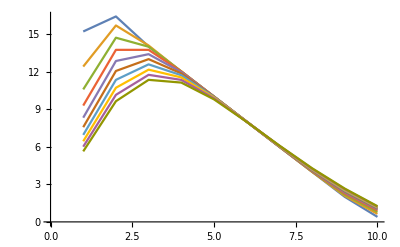

```mathematica
(*3. Redo Problem 1 with ↵=2 and t=0 .001.*)

a=2;
delx=.1;
delt=.001;
l=.2;
u={20,16,14,12,10,8,6,4,2,0};
Matt={};
For[i=0,i<10,i++,
row={};
For[j=0,j<10,j++,
If[i==j,
AppendTo[row,1-2l],
If[i==j-1||j==i-1,
AppendTo[row,l],
AppendTo[row,0]
];
];
];
AppendTo[Matt,row]
];
Print[MatrixForm[Matt]]

un={};
n=10;
For[i=1,i≤n,i++,
var=Matt.u;
u=var;
AppendTo[un,u];
];

Print[un]
ListLinePlot[un]
```

```mathematica
(*Fourier transform code*)

a=.5;
delx=.1;
delt=.01;
l=.5;
u={20,16,14,12,10,8,6,4,2,0};
Matt={};
For[i=0,i<10,i++,
row={};
For[j=0,j<10,j++,
If[i==j,
AppendTo[row,1-2l],
If[i==j-1||j==i-1,
AppendTo[row,l],
AppendTo[row,0]
];
];
];
AppendTo[Matt,row]
];
Print[MatrixForm[Matt]]

un={};
n=10;
For[i=1,i≤n,i++,
var=Matt.u;
u=var;
AppendTo[un,u];
];

Print[un]
ListLinePlot[un]

M=10;
dftm={};
For[k =0, k ≤ M -1, ++k, 
row = {};
For[i =0, i ≤ M-1, ++i,
 
xi = 2*Pi/M * i;
AppendTo[row, E^(I*k*xi)];

];

AppendTo[dftm,row];
];

dftm = Simplify[dftm];

MatrixForm[dftm]
dftm = dftm/Sqrt[M];

c={};
For[i=1,i≤10,i++,
ci=dftm.un[[i]];
AppendTo[c,ci];
];

c = N[c]

M = 10;
interp = {};
Clear[x];
For[k =0, k ≤ M -1, ++k, 

f = 1/Sqrt[M]*(
Re[c[[k+1]]]*Cos[k* 2*Pi/M * x] +
Im[c[[k+1]]]*Sin[k* 2*Pi/M * x]
);
AppendTo[interp, f];

];

(*For every 5 element*)
lis={};
For[i=1,i≤10,i++,
For[j=2,j≤10,j++,
If[j==5,
s=N[c[i][j]]/N[c[i][j-1]];
AppendTo[lis,s];
];
];
];

c=N[c];

plist = {};
For[i =1, i ≤ M,i++,
AppendTo[plist, Show[{Plot[Total[interp[[1;;i]]],{x,0,10}, PlotRange -> {{0,10},{0,1.1}},AspectRatio->.3,ImageSize->Medium],ListPlot[l, Filling->Axis, AspectRatio->Full]}]];
AppendTo[plist,ListPlot[Re[c[[1;;i]]]^2 + Im[c[[1;;i]]]^2,AspectRatio->.3,Filling->Axis,PlotRange -> {{0,10},{0,2}},ImageSize->Medium]]

]
```

(0. | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.5 | 0. | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.5 | 0. | 0.5 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.5 | 0. | 0.5 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.5 | 0. | 0.5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.5 | 0. | 0.5 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.5 | 0. | 0.5 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0. | 0.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0. | 0.5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0.)

{{8.,17.,14.,12.,10.,8.,6.,4.,2.,1.},{8.5,11.,14.5,12.,10.,8.,6.,4.,2.5,1.},{5.5,11.5,11.5,12.25,10.,8.,6.,4.25,2.5,1.25},{5.75,8.5,11.875,10.75,10.125,8.,6.125,4.25,2.75,1.25},{4.25,8.8125,9.625,11.,9.375,8.125,6.125,4.4375,2.75,1.375},{4.40625,6.9375,9.90625,9.5,9.5625,7.75,6.28125,4.4375,2.90625,1.375},{3.46875,7.15625,8.21875,9.73438,8.625,7.92188,6.09375,4.59375,2.90625,1.45313},{3.57813,5.84375,8.44531,8.42188,8.82813,7.35938,6.25781,4.5,3.02344,1.45313},{2.92188,6.01172,7.13281,8.63672,7.89063,7.54297,5.92969,4.64063,2.97656,1.51172},{3.00586,5.02734,7.32422,7.51172,8.08984,6.91016,6.0918,4.45313,3.07617,1.48828}}

-Graphics-

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | (-1)^(1/5) | (-1)^(2/5) | (-1)^(3/5) | (-1)^(4/5) | -1 | -(-1)^(1/5) | -(-1)^(2/5) | -(-1)^(3/5) | -(-1)^(4/5)
1 | (-1)^(2/5) | (-1)^(4/5) | -(-1)^(1/5) | -(-1)^(3/5) | 1 | (-1)^(2/5) | (-1)^(4/5) | -(-1)^(1/5) | -(-1)^(3/5)
1 | (-1)^(3/5) | -(-1)^(1/5) | -(-1)^(4/5) | (-1)^(2/5) | -1 | -(-1)^(3/5) | (-1)^(1/5) | (-1)^(4/5) | -(-1)^(2/5)
1 | (-1)^(4/5) | -(-1)^(3/5) | (-1)^(2/5) | -(-1)^(1/5) | 1 | (-1)^(4/5) | -(-1)^(3/5) | (-1)^(2/5) | -(-1)^(1/5)
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
1 | -(-1)^(1/5) | (-1)^(2/5) | -(-1)^(3/5) | (-1)^(4/5) | 1 | -(-1)^(1/5) | (-1)^(2/5) | -(-1)^(3/5) | (-1)^(4/5)
1 | -(-1)^(2/5) | (-1)^(4/5) | (-1)^(1/5) | -(-1)^(3/5) | -1 | (-1)^(2/5) | -(-1)^(4/5) | -(-1)^(1/5) | (-1)^(3/5)
1 | -(-1)^(3/5) | -(-1)^(1/5) | (-1)^(4/5) | (-1)^(2/5) | 1 | -(-1)^(3/5) | -(-1)^(1/5) | (-1)^(4/5) | (-1)^(2/5)
1 | -(-1)^(4/5) | -(-1)^(3/5) | -(-1)^(2/5) | -(-1)^(1/5) | -1 | (-1)^(4/5) | (-1)^(3/5) | (-1)^(2/5) | (-1)^(1/5))

{{25.9307+0. ⅈ,0.511667+9.73249 ⅈ,0.19544+4.3525 ⅈ,-0.19544+2.29753 ⅈ,-0.511667+1.02749 ⅈ,-0.632456+0. ⅈ,-0.511667-1.02749 ⅈ,-0.19544-2.29753 ⅈ,0.19544-4.3525 ⅈ,0.511667-9.73249 ⅈ},{24.5077+0. ⅈ,-0.767501+8.61725 ⅈ,-0.488599+2.548 ⅈ,0.293159+0.493026 ⅈ,1.27917-0.0877578 ⅈ,1.73925+0. ⅈ,1.27917+0.0877578 ⅈ,0.293159-0.493026 ⅈ,-0.488599-2.548 ⅈ,-0.767501-8.61725 ⅈ},{23.0056+0. ⅈ,-1.86633+7.76146 ⅈ,-0.724408+2.06556 ⅈ,0.166604+1.12584 ⅈ,-0.10569+0.860962 ⅈ,-0.553399+0. ⅈ,-0.10569-0.860962 ⅈ,0.166604-1.12584 ⅈ,-0.724408-2.06556 ⅈ,-1.86633-7.76146 ⅈ},{21.9383+0. ⅈ,-2.41108+6.79031 ⅈ,-0.690226+1.46536 ⅈ,0.0196035+0.479161 ⅈ,0.591405-0.185379 ⅈ,1.22538+0. ⅈ,0.591405+0.185379 ⅈ,0.0196035-0.479161 ⅈ,-0.690226-1.46536 ⅈ,-2.41108-6.79031 ⅈ},{20.8315+0. ⅈ,-2.88377+6.02786 ⅈ,-0.691878+1.31748 ⅈ,0.0772441+0.716589 ⅈ,0.0594227+0.684363 ⅈ,-0.51387+0. ⅈ,0.0594227-0.684363 ⅈ,0.0772441-0.716589 ⅈ,-0.691878-1.31748 ⅈ,-2.88377-6.02786 ⅈ},{19.9421+0. ⅈ,-3.09407+5.27163 ⅈ,-0.638863+1.04622 ⅈ,-0.0336219+0.417657 ⅈ,0.278166-0.158679 ⅈ,0.968448+0. ⅈ,0.278166+0.158679 ⅈ,-0.0336219-0.417657 ⅈ,-0.638863-1.04622 ⅈ,-3.09407-5.27163 ⅈ},{19.028+0. ⅈ,-3.28419+4.67434 ⅈ,-0.630115+0.98589 ⅈ,0.00827197+0.533528 ⅈ,0.121186+0.537878 ⅈ,-0.489165+0. ⅈ,0.121186-0.537878 ⅈ,0.00827197-0.533528 ⅈ,-0.630115-0.98589 ⅈ,-3.28419-4.67434 ⅈ},{18.2498+0. ⅈ,-3.33044+4.10399 ⅈ,-0.593958+0.826271 ⅈ,-0.0628327+0.356745 ⅈ,0.115911-0.112777 ⅈ,0.807863+0. ⅈ,0.115911+0.112777 ⅈ,-0.0628327-0.356745 ⅈ,-0.593958-0.826271 ⅈ,-3.33044-4.10399 ⅈ},{17.4543+0. ⅈ,-3.38184+3.65274 ⅈ,-0.588129+0.793393 ⅈ,-0.0355161+0.427821 ⅈ,0.134169+0.423779 ⅈ,-0.471871+0. ⅈ,0.134169-0.423779 ⅈ,-0.0355161-0.427821 ⅈ,-0.588129-0.793393 ⅈ,-3.38184-3.65274 ⅈ},{16.7533+0. ⅈ,-3.34875+3.22668 ⅈ,-0.563528+0.68455 ⅈ,-0.0852862+0.307174 ⅈ,0.0261879-0.0712938 ⅈ,0.694836+0. ⅈ,0.0261879+0.0712938 ⅈ,-0.0852862-0.307174 ⅈ,-0.563528-0.68455 ⅈ,-3.34875-3.22668 ⅈ}}

ListPlot::lpn: 0.5 is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{,ListPlot[0.5,Filling→Axis,AspectRatio→Full]}].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.